```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,475,500,530};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

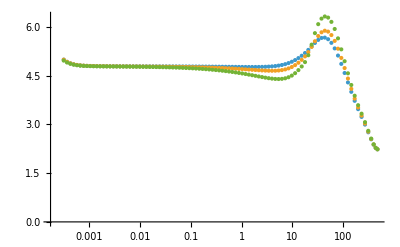

```mathematica
ListPlot[fitdata[[-3;;-1]],PlotRange->All,ScalingFunctions->{"Log"}]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]](*,InterpolationOrder->1*)],{i,1,Length[mub]}];
```

```mathematica
T0p01=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-4.79)/4.79]==0.01,{x,0.01,0.0001,40}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p01.dat",T0p01];
T0p02=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-4.79)/4.79]==0.02,{x,0.01,0.0001,40}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p02.dat",T0p02];
T0p03=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-4.79)/4.79]==0.03,{x,5,0.0001,40}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p03.dat",T0p03];
```

FindRoot::jsing: 在点 {x} = {1.55723} 碰到奇异雅克比. 尝试扰动初始点.

{0.325609,0.326049,0.343457,0.334392,0.343457,0.35976,0.390905,0.460562,0.681095,2.40131,1.55723,0.27696,0.055765}

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

{0.8393,0.841288,0.884844,0.861841,0.884844,0.925138,1.0012,1.16878,1.66951,4.3719,8.4477,1.10936,0.201752}

FindRoot::jsing: 在点 {x} = {3.94178} 碰到奇异雅克比. 尝试扰动初始点.

{1.46936,1.47302,1.54755,1.50818,1.54755,1.61589,1.74346,2.01938,2.80127,6.11825,9.99587,3.94178,0.427216}